Cylinder with radius RR, scattering from the left, delta potential with strength UU at x = 0.
Δ Ψ(θ, r, z) = E Ψ(θ, r, z)
Separate variables: Ψ_m(θ, r, z) = exp(I m θ)

Solutions of radial equation:

```mathematica
rr := 1
RR := 2
mm := 0
uu := -1
```

```mathematica
N[BesselJZero[1, 1]]
```

3.83171

```mathematica
phi[n_, r_] := (√2)/(RR BesselJ[Abs[mm] + 1,BesselJZero[mm,n]])BesselJ[mm,BesselJZero[mm,n] r/RR]
```

```mathematica
N[Integrate[r * phi[1, r] * phi[2, r], {r, 0, RR}]]
N[Integrate[r * phi[2, r] * phi[2, r], {r, 0, RR}]]
```

0.

1.

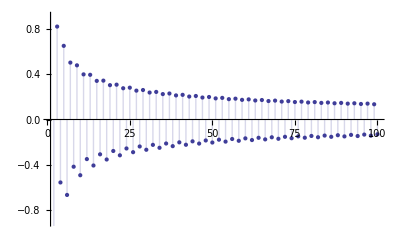

```mathematica
DiscretePlot[N[Integrate[phi[1, r] * phi[n, r], {r, 0, rr}]], {n, 1, 100}]
```

```mathematica
phiEn[n_] := (BesselJZero[mm, n]/RR)^2
```

```mathematica
kk[En_, n_] := Sqrt[En - phiEn[n]]
```

```mathematica
Refl[En_, n_] := (2 kk[En, n])/(2 kk[En, n] + I uu)
Trans[En_, n_] := (- I uu)/(2 kk[En, n] + I uu)
```

```mathematica
Trans2[En_] := Norm[Trans[En, 1]] + Norm[Trans[En, 2]]
```

```mathematica
N[Trans2[30.1]]
```

4.6749

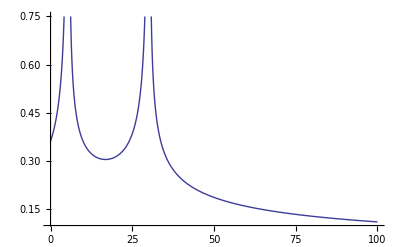

```mathematica
Plot[Trans2[EE], {EE, 0.0, 100.0}]
```

```mathematica
N[Abs[Trans2[30.2213]]]
```

13277.5

```mathematica
FindMaximum[Abs[Trans2[EE]],{EE,30.0}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4.70757×10^6,{EE→30.2213}}

```mathematica
Plot3D[Abs[Trans[x + I y, 1]], {x, 0.0, 10.0}, {y, -10.0, 10.0}, ImageSize->Full]
```

-Graphics3D-

```mathematica
N[phiEn[2]]
```

30.4713

```mathematica
psi1[n_, r_, z_] := Exp[I  kk[En, n] z] phi[n, r] + Refl[En, n] Exp[-I kk[En, n]z] phi[n, r]
psi2[n_, r_, z_] := Trans[En, n] Exp[I kk[En, n] z] * phi[n, r]
psi[n_, r_, z_] := If[z < 0, psi1[n, r, z], psi2[n, r, z]]
```

```mathematica
En := 10.0
```

3.64744

```mathematica
Plot3D[Norm[psi[1, r, z]]^2,{z,-10.0,10.0},{r,0,RR}]
```

-Graphics3D-

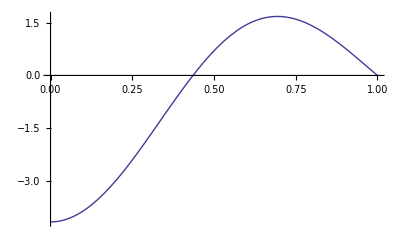

```mathematica
Plot[phi[2, r], {r, 0, RR}]
```

```mathematica
N[En[2]]
```

30.4713